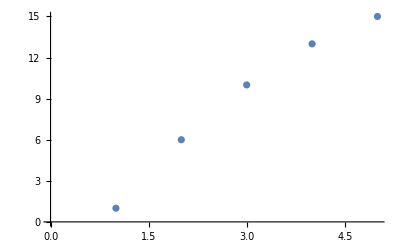

```mathematica
(* 01 *)
```

```mathematica
(* 02 *)
%
```

-Graphics-

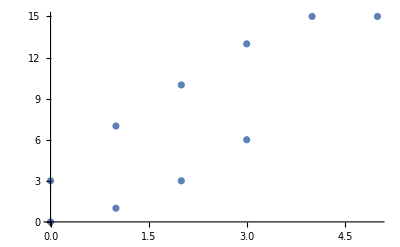

```mathematica
(* 03 *)
res1 = {{0,0},{1,1},{2,3},{3,6},{5,15}};
res2 = {{0,3},{1,7},{2,10},{3,13},{4,15},{5,16}};
Show[ListPlot[res1],ListPlot[res2]]
```

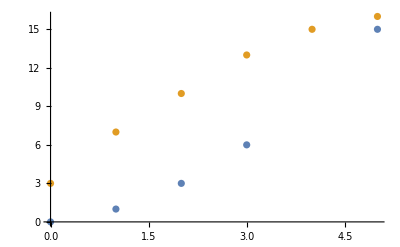

```mathematica
ListPlot[{
res1,res2
}]
```

```mathematica
(* 04 *)
Manipulate[
ListPlot[{{1,1},{2,i},{3,10}},PlotRange->{0,20}],
{i,1,15}
]
```

```mathematica
(* 05 *)
```

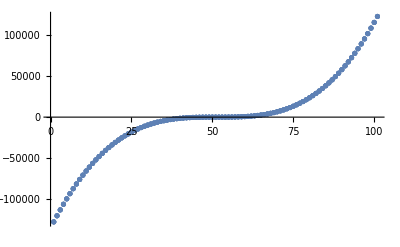

```mathematica
points17 = Table[i^3-i^2+1,{i,-50,50}];
ListPlot[points17,Mesh->Full]
```

```mathematica
(* 06 *)
points21 = Table[Cos[a]+Sin[b],{a,-10,10},{b,-10,10}];
ListPlot3D[points21,Mesh->None]
```

-Graphics3D-

```mathematica
(* 07 *)
points21 = Table[Cos[a]+Sin[b],{a,-10,10,0.1},{b,-10,10,0.1}];
ListPlot3D[points21,Mesh->None]
```

-Graphics3D-

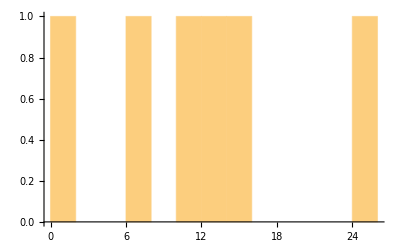

```mathematica
(* 08 *)
Histogram[{1,6,10,13,15,25},12]
```

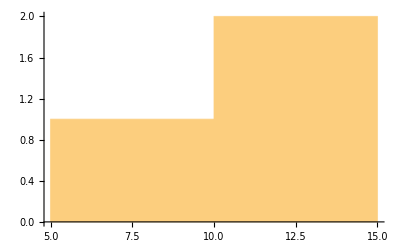

```mathematica
(* 09 *)
Histogram[{1,6,10,13,15,25},{{5,10,15}}]
```

```mathematica
(* 10 *)
Manipulate[
ThermometerGauge[6x,{0,20}],
{x,1,3,0.1}
]
```